silicon, cramped or free  @ both ends
b vs Q^-1 (L=10 b)

300K

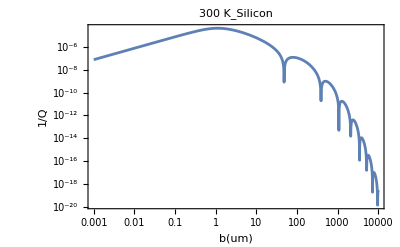

```mathematica
Qr300=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(1/2)/(10 √lT)}/.
{d->1.3,lT->1.257 10^-2,an->4.73,ΔE->7.942 10^-5};

Qr300g=LogLogPlot[Qr300,{b,0.001,10000},PlotLabel->300K_Silicon, Frame->True,FrameLabel->{b[um],Q^-1}]
```

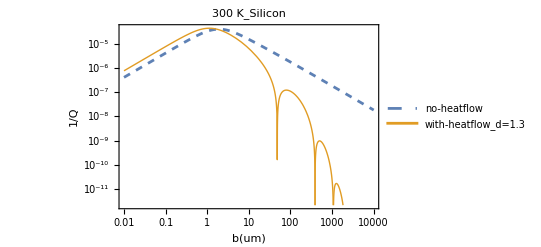

```mathematica
QNor300 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(1/2)/(10 √lT)}/.
{d->1.3,lT->1.257 10^-2,an->4.73,ΔE->7.942 10^-5};
Qr300g=LogLogPlot[{QNor300,Qr300},{b,0.01,10000},PlotLabel->300K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.3,0.25}],Frame->True,FrameLabel->{b[um],Q^-1}]
```

100K

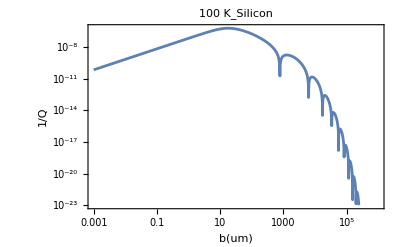

```mathematica
Qr100=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(1/2)/(10 √lT)}/.
{d->1.3,lT->2.017 10^-1,an->4.73,ΔE->1.232 10^-6};

Qr100g=LogLogPlot[Qr100,{b,0.001,1000000},PlotLabel->100K_Silicon, Frame->True,FrameLabel->{b[um],Q^-1}]
```

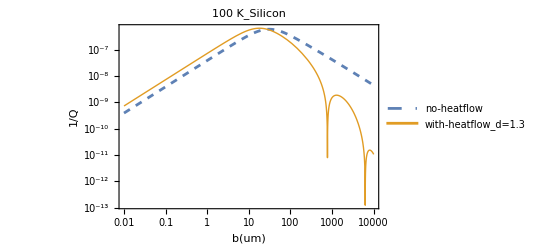

```mathematica
QNor100 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(1/2)/(10 √lT)}/.
{d->1.3,lT->2.017 10^-1,an->4.73,ΔE->1.232 10^-6};
QNor100g=LogLogPlot[{QNor100,Qr100},{b,0.01,10000},PlotLabel->100K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.3,0.25}],Frame->True,FrameLabel->{b[um],Q^-1}]
```

10K

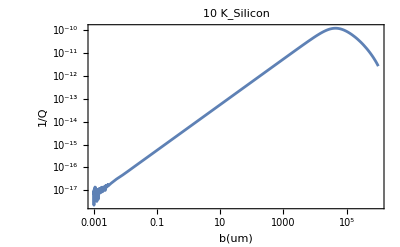

```mathematica
Qr10=Abs[3/(4 ξ^3)-ΔE/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{ξ->an/(4 3^(1/4))b^(1/2)/(10 √lT)}/.
{d->1.3,lT->4.977 10^2,an->4.73,ΔE->2.319 10^-10};
Qr10g=LogLogPlot[Qr10,{b,0.001,1000000},PlotLabel->10K_Silicon, Frame->True,FrameLabel->{b[um],Q^-1}]
```

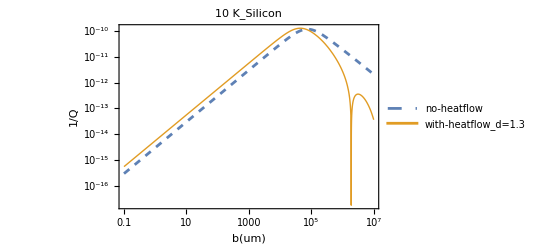

```mathematica
QNor10 =Abs[ ΔE(6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) )]/.
{ξ->an/(4 3^(1/4))b^(1/2)/(10 √lT)}/.
{d->1.3,lT->4.977 10^2,an->4.73,ΔE->2.319 10^-10};
QNor10g=LogLogPlot[{QNor10,Qr10},{b,0.1,10000000},PlotLabel->10K_Silicon, PlotStyle->{Dashed,Thick},PlotLegends->Placed[{"no-heatflow","with-heatflow_d=1.3"},{0.5,0.25}],Frame->True,FrameLabel->{b[um],Q^-1}]
```

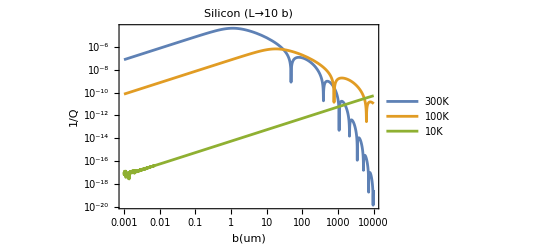

```mathematica
LogLogPlot[{Qr300,Qr100,Qr10},{b,0.001,10000},PlotLabel-> Silicon ( L->10b), Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.6,0.2}],FrameLabel->{b[um],Q^-1}]
```

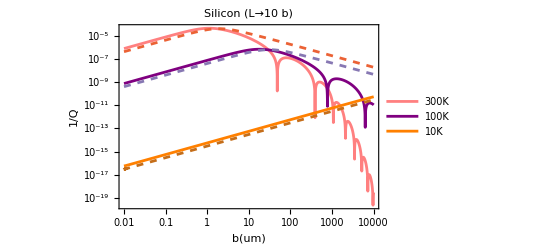

```mathematica
LogLogPlot[{Qr300,Qr100,Qr10,QNor300,QNor100,QNor10},{b,0.01,10000},PlotLabel-> Silicon ( L->10b),PlotStyle->{Pink,Purple,Orange,Dashed,Dashed,Dashed},  Frame->True,PlotLegends->Placed[{"300K","100K","10K"},{0.6,0.2}],FrameLabel->{b[um],Q^-1}]
```